```mathematica
PBC = False;
hermitian = True;

NUnit = 8;

systemLengthX = NUnit;
systemLengthY = NUnit;
systemLengthZ = 4;


coordConvention=Flatten[{Flatten[Table[{x,y,z,1},{x,1,NUnit},{y,1,NUnit},{z,1,systemLengthZ}],2],Flatten[Table[{x,y,z,2},{x,1,NUnit},{y,1,NUnit},{z,1,systemLengthZ}],2]},1];
```

```mathematica
appliedVoltage = 1;
RShunt = 50;

frequency = 2.5*10^6;
driveFreq = 2π*frequency;

L1Value = 27*10^-6;
L2Value = 5.6*10^-6;
L3Value = 27*10^-6;

C1Value = 150*10^-12;
C2Value = 75*10^-12;
C3Value = 150*10^-12;

Ry = 15.92;


inputRow =1;
inputColumn = 1;
inputHeight = 1;

InputNodes ={{inputRow,inputColumn,inputHeight,1},{inputRow,inputColumn,inputHeight,2}};

inputPos ={Position[coordConvention,{inputRow,inputColumn,1,1}][[1,1]],Position[coordConvention,{inputRow,inputColumn,1,2}][[1,1]]};
```

```mathematica
circuitGroundMatrixFourier = Table[Which[x==y,Which[coordConvention[[x,4]]==1,(I*driveFreq*L2Value)^-1+If[PBC==False,If[coordConvention[[x,3]]==1 ||coordConvention[[x,3]]==systemLengthZ,I*driveFreq*C1Value,0],0],
coordConvention[[x,4]]==2,(I*driveFreq*L3Value)^-1+If[PBC==False,If[coordConvention[[x,3]]==1 ||coordConvention[[x,3]]==systemLengthZ,I*driveFreq*C1Value,0],0],True,0],True,0],{x,1,Length[coordConvention]},{y,1,Length[coordConvention]}];

adjacencyMatrixXToYSameCellFourier= Table[Which[
coordConvention[[x]]==coordConvention[[y]]-{0,0,0,1}||
coordConvention[[x]]==coordConvention[[y]]+{0,0,0,1},I*driveFreq*C1Value,
True,0],{x,1,Length[coordConvention]},{y,1,Length[coordConvention]}];
 
adjacencyMatrixXToYDifferentCellFourier = Table[Which[
coordConvention[[x]]==Flatten[{Mod[coordConvention[[y,{1,2}]]+{-1,1},NUnit,1],Mod[coordConvention[[y,3]]+0,systemLengthZ,1],Mod[coordConvention[[y,4]]+1,2,1]}] ||
coordConvention[[x]]==Flatten[{Mod[coordConvention[[y,{1,2}]]-{-1,1},NUnit,1],Mod[coordConvention[[y,3]]-0,systemLengthZ,1],Mod[coordConvention[[y,4]]-1,2,1]}]||
coordConvention[[x]]==Flatten[{Mod[coordConvention[[y,{1,2}]]+{1,-1},NUnit,1],Mod[coordConvention[[y,3]]+0,systemLengthZ,1],Mod[coordConvention[[y,4]]+1,2,1]}]||
coordConvention[[x]]==Flatten[{Mod[coordConvention[[y,{1,2}]]-{1,-1},NUnit,1],Mod[coordConvention[[y,3]]-0,systemLengthZ,1],Mod[coordConvention[[y,4]]-1,2,1]}],I*driveFreq*C2Value,
True,0],{x,1,Length[coordConvention]},{y,1,Length[coordConvention]}];

adjacencyMatrixXToXFourier = Table[Which[
coordConvention[[x]]==Mod[coordConvention[[y]]+{0,1,0,0},8,1] ||
coordConvention[[x]]==Mod[coordConvention[[y]]-{0,1,0,0} ,8,1]
,Which[
coordConvention[[x,4]]==1,I*driveFreq*C3Value,
coordConvention[[x,4]]==2,(I*driveFreq*L1Value)^-1,
coordConvention[[x]]==Mod[coordConvention[[y]]+{1,0,0,0},8,1] ||
coordConvention[[x]]==Mod[coordConvention[[y]]-{1,0,0,0} ,8,1]
,If[hermitian==False,Ry^-1,0],
True,0],True,0],{x,1,Length[coordConvention]},{y,1,Length[coordConvention]}];

adjacencyMatrixZ=
Table[
Which[
!coordConvention[[x,3]]==1 &&!coordConvention[[y,3]]==systemLengthZ &&!coordConvention[[y,3]]==1 &&!coordConvention[[x,3]]==systemLengthZ,
Which[coordConvention[[x]]==coordConvention[[y]] + {0, 0, 1, -1} ||coordConvention[[x]]==coordConvention[[y]] + {0, 0, 1, 1} ||coordConvention[[x]]==coordConvention[[y]] - {0, 0, 1, -1}||coordConvention[[x]]==coordConvention[[y]] - {0, 0, 1, 1} ,I*driveFreq*C1Value,
True,0]
,
coordConvention[[x,3]]==1 &&!coordConvention[[y,3]]==systemLengthZ ||coordConvention[[y,3]]==1 &&!coordConvention[[x,3]]==systemLengthZ,Which[coordConvention[[x]]==coordConvention[[y]] - {0, 0, 1, -1} ||coordConvention[[x]]==coordConvention[[y]] - {0, 0, 1, 1}||coordConvention[[x]]==coordConvention[[y]] + {0, 0, 1, -1} ||coordConvention[[x]]==coordConvention[[y]] + {0, 0, 1, 1} ,I*driveFreq*C1Value,True,0]
,
coordConvention[[x,3]]==systemLengthZ &&!coordConvention[[y,3]]==1||coordConvention[[y,3]]==systemLengthZ &&!coordConvention[[x,3]]==1

,Which[coordConvention[[x]]==coordConvention[[y]] - {0, 0, 1, -1} ||coordConvention[[x]]==coordConvention[[y]] - {0, 0, 1, 1}||coordConvention[[x]]==coordConvention[[y]] + {0, 0, 1, -1} ||coordConvention[[x]]==coordConvention[[y]] + {0, 0, 1, 1} ,I*driveFreq*C1Value,True,0]
,True,0]
  , {x, 1, Length[coordConvention]}, {y, 1, Length[coordConvention]}];

totalNodeConductanceMatrixFourier = Table[
Which[x==y,
Which[coordConvention[[x,4]]==1,
2*I*driveFreq*C3Value+2*I*driveFreq*C2Value+If[hermitian==False,2 Ry^-1,0]+If[coordConvention[[x,3]]==1 ||coordConvention[[x,3]]==systemLengthZ,I*driveFreq*C1Value,2*I*driveFreq*C1Value],

coordConvention[[x,4]]==2,2*I*driveFreq*C2Value+2*(I*driveFreq*L1Value)^-1+If[hermitian==False,2 Ry^-1,0]+
If[coordConvention[[x,3]]==1 ||coordConvention[[x,3]]==systemLengthZ,I*driveFreq*C1Value,2*I*driveFreq*C1Value]
,True,0],True,0],{x,1,Length[coordConvention]},{y,1,Length[coordConvention]}];
```

```mathematica
laplacianMatrixFourier= totalNodeConductanceMatrixFourier-(adjacencyMatrixXToXFourier+adjacencyMatrixXToYDifferentCellFourier+adjacencyMatrixXToYSameCellFourier+adjacencyMatrixZ)+circuitGroundMatrixFourier;

inverseLaplacianMatrixFourier= Inverse[laplacianMatrixFourier];
```

```mathematica
currentVectorDynamic = Table[Which[coordConvention[[node]]=={3,3,1,2},Exp[-I*0],
coordConvention[[node]]=={2,3,1,2},Exp[-I*π/2],True,0],{node, 1,Length[coordConvention]}];

dynamicVoltages =Dot[currentVectorDynamic,inverseLaplacianMatrixFourier];
```

```mathematica
vertiSubs=Flatten[Table[{z, sub}, {z, 1, systemLengthZ}, {sub, 1, 2}],1];

currentVectorOBC = Table[If[coordConvention[[node]] == Flatten[{InputNodes[[vertiSubs[[vz,2]], {1, 2}]], vertiSubs[[vz,1]], InputNodes[[vertiSubs[[vz,2]], 4]]}], appliedVoltage/(RShunt + inverseLaplacianMatrixFourier[[node, node]]), 0], {vz, 1, Dimensions[vertiSubs][[1]]}, {node, 1, Length[coordConvention]}];

OBCVoltages = Table[Dot[currentVectorOBC[[vz]], inverseLaplacianMatrixFourier],{vz, 1, Dimensions[vertiSubs][[1]]}];
```

```mathematica
fourierVoltagesOBC = Table[∑_(l=1)^NUnit ( ∑_(j=1)^NUnit OBCVoltages[[vz,((vertiSubs[[uvz,2]]-1)*NUnit^2*systemLengthZ)+((j-1)*NUnit*systemLengthZ)+((l-1)*systemLengthZ)+vertiSubs[[uvz,1]]]]*Exp[-ⅈ*2*π*kx*(j)/NUnit])*Exp[-ⅈ*2*π*ky*(l)/NUnit],{vz, 1, Dimensions[vertiSubs][[1]]},{uvz, 1, Dimensions[vertiSubs][[1]]},{kx,1,NUnit},{ky,1,NUnit}];

fourierCurrentVectorOBC = Table[∑_(l=1)^NUnit ( ∑_(j=1)^NUnit currentVectorOBC[[vz,((vertiSubs[[vz,2]]-1)*NUnit^2*systemLengthZ)+((j-1)*NUnit*systemLengthZ)+((l-1)*systemLengthZ)+vertiSubs[[vz,1]]]]*Exp[-ⅈ*2*π*kx*(j)/NUnit])*Exp[-ⅈ*2*π*ky*(l)/NUnit],{vz,1,Dimensions[vertiSubs][[1]]},{kx,1,NUnit},{ky,1,NUnit}];
```

```mathematica
GreensOBC = Table[(fourierVoltagesOBC[[vz,uvz,kx,ky]])/(fourierCurrentVectorOBC[[uvz,kx,ky]]),{vz, 1, Dimensions[vertiSubs][[1]]},{uvz, 1, Dimensions[vertiSubs][[1]]},{kx,1,NUnit},{ky,1,NUnit}];
```

```mathematica
(*OBCHamZ[{kx_,ky_},z_]:=Sum[1/systemLengthZ *( {
{2C1Value+2C2Value+2C3Value,0},
{0,2C1Value+2C2Value-2/((2π*frequency)^2 L1Value)}
}-{
{2*C3Value*Cos[ky],C1Value+C1Value*Exp[I*kz]+2C2Value*Cos[ky-kx]},{C1Value+C1Value*Exp[-I*kz]+2C2Value*Cos[ky-kx],-2/((2π*frequency)^2*L1Value)Cos[ky]}
}+{
{-1/((2π*frequency)^2 L2Value),0},
{0,-1/((2π*frequency)^2 L3Value)}
})*Exp[I*kz*z],{kz,0,(systemLengthZ-1)2π/systemLengthZ,2π/systemLengthZ}];*)
Omega = 2*π*frequency;
LBZ = L1Value;
C1 = Omega*C1Value;
CAz = C1;
Cy = C1/2;
Alpha = Omega/(Omega^2*LBZ);

Xi={PauliMatrix[0],PauliMatrix[1],PauliMatrix[2],PauliMatrix[3]};
X[Mu_]:=Xi[[Mu+1]]

OBCHamZ[{kx_,ky_},z_]:=Sum[1/systemLengthZ *(N[(-(CAz-Alpha)Cos[ky]) X[0]-(C1 (1+Cos[kz])+Cy *(2 Cos[ky-kx])) X[1]-C1 Sin[kz] X[2]-(CAz+Alpha) Cos[ky] X[3]])*Exp[I*kz*z],{kz,0,(systemLengthZ-1)2π/systemLengthZ,2π/systemLengthZ}];

OBCHam[kx_,ky_] :=ArrayFlatten[Table[Which[xpos == ypos,OBCHamZ[{kx,ky},0],xpos == ypos +1,OBCHamZ[{kx,ky},1],xpos == ypos-1,OBCHamZ[{kx,ky},-1],True,0],{xpos,1,systemLengthZ},{ypos,1,systemLengthZ}]];
```

```mathematica
PathCoordX = Join[Subdivide[0,0,2],Subdivide[Pi/4,Pi,3],Subdivide[Pi,Pi,3],Subdivide[(5π)/4,2Pi,3],Subdivide[2Pi,2Pi,1]];
PathCoordY = Join[Subdivide[2π,(3Pi)/2,2],Subdivide[(3Pi)/2,(3Pi)/2,3],Subdivide[(7Pi)/4,2π,1],Subdivide[π/4,π/2,1],Subdivide[Pi/2,Pi/2,3],Subdivide[Pi/4,0,1]];
```

```mathematica
LapEigenvaluesOBC = Im[Table[SortBy[Eigenvalues[Inverse[GreensOBC[[;;,;;,If[NUnit/(2π)PathCoordX[[i]]==0,8,NUnit/(2π)PathCoordX[[i]]],If[NUnit/(2π)PathCoordY[[i]]==0,8,NUnit/(2π)PathCoordY[[i]]]]]]],Im],{i,1,Length[PathCoordX]}]];

dataEigenvaluesOBC = Re[Table[SortBy[Eigenvalues[OBCHam[PathCoordX[[i]],PathCoordY[[i]]]],Re],{i,1,Length[PathCoordX]}]];
```

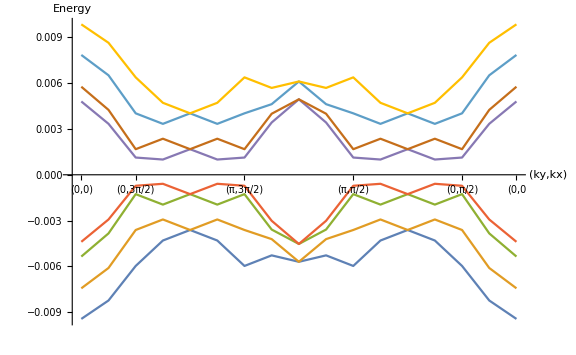

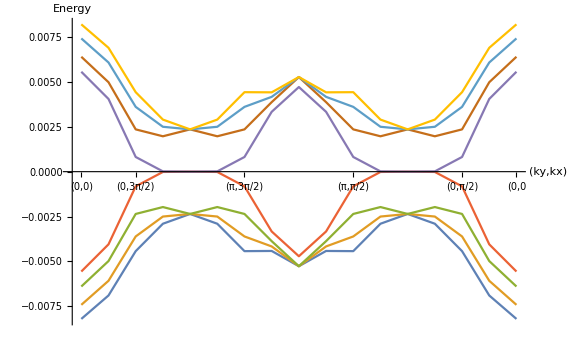

```mathematica
ListLinePlot[Transpose[LapEigenvaluesOBC],AxesLabel->{"(ky,kx)","Energy"},PlotRange->All,ImageSize->Large,Ticks->{{{1,"(0,0)"},{3,"(0,3π/2)"},{7,"(π,3π/2)"},{11,"(π,π/2)"},{15,"(0,π/2)"},{17,"(0,0"}},Automatic}]

ListLinePlot[Transpose[dataEigenvaluesOBC],AxesLabel->{"(ky,kx)","Energy"},PlotRange->All,ImageSize->Large,Ticks->{{{1,"(0,0)"},{3,"(0,3π/2)"},{7,"(π,3π/2)"},{11,"(π,π/2)"},{15,"(0,π/2)"},{17,"(0,0"}},Automatic}]
```

```mathematica
ampl = Table[
Abs[dynamicVoltages[[((sub-1)*NUnit^2*systemLengthZ)+((x-1)*NUnit*systemLengthZ)+((y-1)*systemLengthZ)+2]]]
,{x,1,8},{y,1,8},{sub,1,2}];

phas = Table[
Mod[Arg[dynamicVoltages[[((sub-1)*NUnit^2*systemLengthZ)+((x-1)*NUnit*systemLengthZ)+((y-1)*systemLengthZ)+1]]-dynamicVoltages[[((2-1)*NUnit^2*systemLengthZ)+((2-1)*NUnit*systemLengthZ)+((3-1)*systemLengthZ)+1]]],2π]
,{x,1,8},{y,1,8},{sub,1,2}];

phasTheo = Table[
Mod[-(x-2)*π/2*(sub-2),2π]
,{x,1,8},{y,1,8},{sub,1,2}];

maxAmpl = {Max[Flatten[ampl[[;;,;;,1]]]],Max[Flatten[ampl[[;;,;;,2]]]]};

coloredPulse = Table[
RGBColor[(phas[[x,y,sub]])/(2π),0,1-(phas[[x,y,sub]])/(2π)]
,{x,1,8},{y,1,8},{sub,1,2}];

gradientPulse = Table[
RGBColor[0,0,0,(ampl[[x,y,sub]])/maxAmpl[[sub]]]
,{x,1,8},{y,1,8},{sub,1,2}];
```

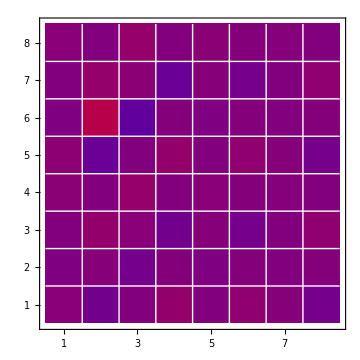
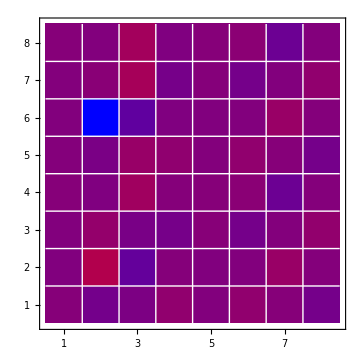
| Simulated Phase Behaviour of Surface Pulse | 
Sublattice A |  | Sublattice B
-Graphics- |  | -Graphics-

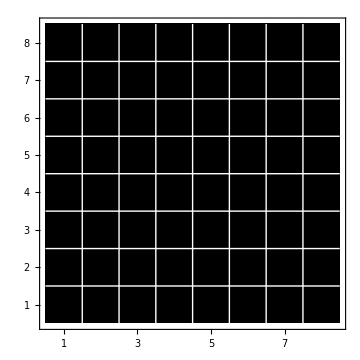

```mathematica
cells = Block[{reverseRange = Reverse[Range[8]]},
Table[{reverseRange[[i]],i},
{i,8}
]];
cells2 = Block[{range = Range[8]},Table[
{range[[i]],i},
{i,8}
]];

Grid[{{"",Text[Style["Simulated Phase Behaviour of Surface Pulse",FontSize->15]],""},{"Sublattice A","","Sublattice B"},{ArrayPlot[Transpose[coloredPulse][[;;,;;,1]],Mesh->{7,7},MeshStyle-> White,AspectRatio->1,Frame->True,FrameTicks->{cells,cells2},ImageSize->Medium]
,
BarLegend[{{RGBColor[1,0,0],RGBColor[0,0,1]},{0,2π}},LegendLayout->"Column",LegendLabel->"Phase of Node"]
,
ArrayPlot[Transpose[coloredPulse][[;;,;;,2]],Mesh->{7,7},MeshStyle-> White,AspectRatio->1,Frame->True,FrameTicks->{cells,cells2},ImageSize->Medium]}}]

ArrayPlot[Transpose[gradientPulse][[;;,;;,1]],Mesh->{7,7},MeshStyle-> White,AspectRatio->1,Frame->True,FrameTicks->{cells,cells2},ImageSize->Medium]
```